```mathematica
SetDirectory[NotebookDirectory[]];
pblue=RGBColor[1,0,0,0.65];
pyellow=RGBColor[1,1,0,0.65];
pred=RGBColor[173/255,216/255,230/255,0.65];
pgreen=RGBColor[1,0,1,0.65];
thr=Pi/8;
cf=Piecewise[{{White,#<-thr},{Blend[{pblue,pgreen},(#+thr)/(thr)],#≤0},{Blend[{pgreen,pred},(#)/(thr)],#≤thr},{White,#>thr}}]&;
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
phase[args:{_?NumericQ..}]:=Module[{},args+Prepend[2Pi Accumulate@-IntegerPart@Differences[args/Pi],0]];
```

```mathematica
file="data/test3";
strlst=ReadList[file<>".out",String];
lst=ToExpression[StringSplit[First[strlst]]]
n=2+lst[[1]];
tmax=lst[[2]];
dt=lst[[3]];
Nt=tmax/dt;
Import[file<>"meanphase.dat"]
frequencies=Flatten[Import[file<>"frequencies.dat"]];
AbsoluteTiming[dat=Partition[BinaryReadList[file<>".dat","Real64"],n]];
data=Transpose[dat[[1;;Length[dat]]],{2,1}];
```

{100,500.,0.01,1.,0.95,5.}

{{100,0.95,5.,1.,1,0.627408,0.289556,0.141242},{100,0.95,5.,1.,1,0.500105,0.201428,0.14129},{100,0.95,5.,1.,1,0.500105,0.201428,0.14129},{100,0.95,5.,1.,1,0.627408,0.289556,0.141242}}

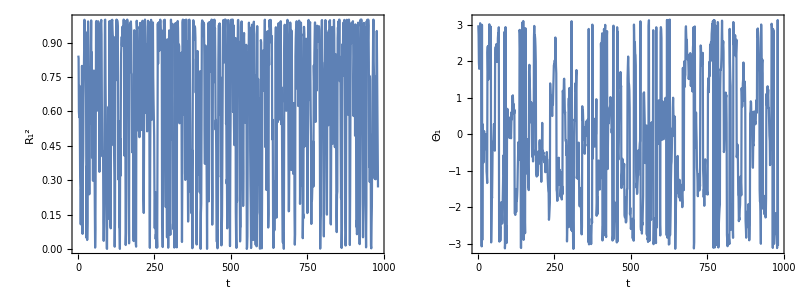

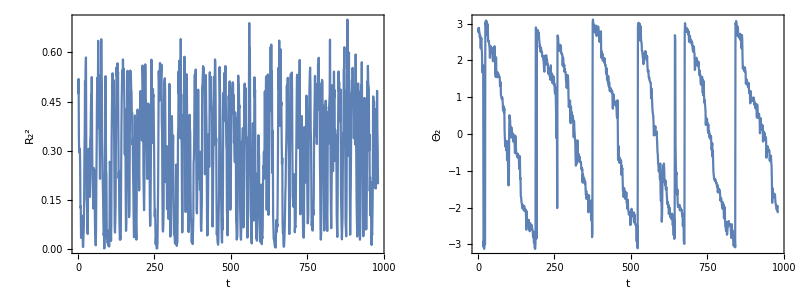

-Graphics-

```mathematica
Nmax=500;
Grid[{{ListPlot[Abs[Total[Exp[I*data[[1;;2,1;;-1;;Ceiling[Length[data[[1]]]/1000]]]]]/(2)]^2,Joined->True,Axes->False,Frame->True,FrameLabel->{t,Subscript[R,1]^2},LabelStyle->Directive[16],Joined->True,PlotRange->All,RotateLabel->False,ImageSize->300],ListPlot[Arg[Total[Exp[I*data[[1;;2,1;;-1;;Ceiling[Length[data[[1]]]/1000]]]]]/(2)],Joined->True,Axes->False,Frame->True,FrameLabel->{t,Subscript[Θ,1]},LabelStyle->Directive[16],Joined->True,PlotRange->All,RotateLabel->False,ImageSize->300]}}]
Grid[{{ListPlot[Abs[Total[Exp[I*data[[3;;-1,1;;-1;;Ceiling[Length[data[[1]]]/1000]]]]]/(Length[data]-2)]^2,Joined->True,Axes->False,Frame->True,FrameLabel->{t,Subscript[R,2]^2},LabelStyle->Directive[16],Joined->True,PlotRange->All,RotateLabel->False,ImageSize->300],ListPlot[Arg[Total[Exp[I*data[[3;;-1,1;;-1;;Ceiling[Length[data[[1]]]/1000]]]]]/(Length[data]-2)],Joined->True,Axes->False,Frame->True,FrameLabel->{t,Subscript[Θ,2]},LabelStyle->Directive[16],Joined->True,PlotRange->All,RotateLabel->False,ImageSize->300]}}]
rasterizeBackground[ListDensityPlot[Transpose[Pi+#-Arg[Total[Exp[I*data[[3;;-1,1;;-1;;Ceiling[Nt/Nmax]]]]]]&/@Reverse[SortBy[data[[3;;-1,1;;-1;;Ceiling[Nt/Nmax]]],Last]]],InterpolationOrder->0,PlotRange->All,AspectRatio->1,ColorFunctionScaling->False,ColorFunction->(cf[Mod[#,2*Pi]-Pi]&),FrameTicks->{{Table[{i,Floor[Nt/Nmax*i*dt]},{i,0,Nmax,Nmax/5}],Table[{i,""},{i,0,Length[data[[1]]],Floor[Length[data[[1]]]/5]}]},{Table[i,{i,0,n,Floor[n/5]}],Table[{i,""},{i,0,n,Floor[n/5]}]}},FrameLabel->{{t,None},{i,file}},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[24,Black],ImageSize->370,ImagePadding->{{75,25},{75,55}}]]
```

```mathematica
table={};
Monitor[Do[
filebase="data/noise/"<>ToString[j]<>"/";
AppendTo[table,{Table[Import[filebase<>"uncorrelated"<>ToString[i]<>"meanphase.dat"][[-1,{3,8}]],{i,1,100}],Table[Import[filebase<>"correlated"<>ToString[i]<>"meanphase.dat"][[-1,{3,8}]],{i,1,100}],Table[#+{0,-0.01}&@(Import[filebase<>"noiseless"<>ToString[i]<>"meanphase.dat"][[-1,{3,8}]]),{i,1,100}]}];,{j,11,20}],j]
```

```mathematica
filebase="data/noise/"<>ToString[17]<>"/";
strlst=ReadList[filebase<>"correlated50.out",String];
lst=StringSplit[First[strlst]]
n=2+ToExpression[lst[[2]]];
delta=ToExpression[lst[[6]]];
dt=Internal`StringToDouble[lst[[10]]];
Nt=Floor[Internal`StringToDouble[lst[[8]]]/dt];
n0=Floor[Internal`StringToDouble[lst[[9]]]/dt];
t1=Internal`StringToDouble[lst[[8]]];
t2=Internal`StringToDouble[lst[[9]]];
data1=Transpose[Partition[BinaryReadList[filebase<>"correlated50.dat","Real64"],n],{2,1}];
frequencies1=Flatten[Import[filebase<>"correlated50frequencies.dat"]];
data2=Transpose[Partition[BinaryReadList[filebase<>"uncorrelated50.dat","Real64"],n],{2,1}];
frequencies2=Flatten[Import[filebase<>"uncorrelated50frequencies.dat"]];
```

{./noiseslave,500,0.95,5.00000000000000000000,0.0,1.0,1,5e2,1e2,1,1e-4,17,rkf45,data/noise/17/correlated50,1}

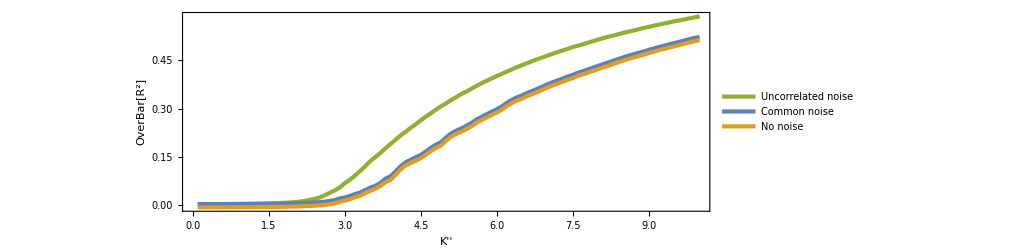
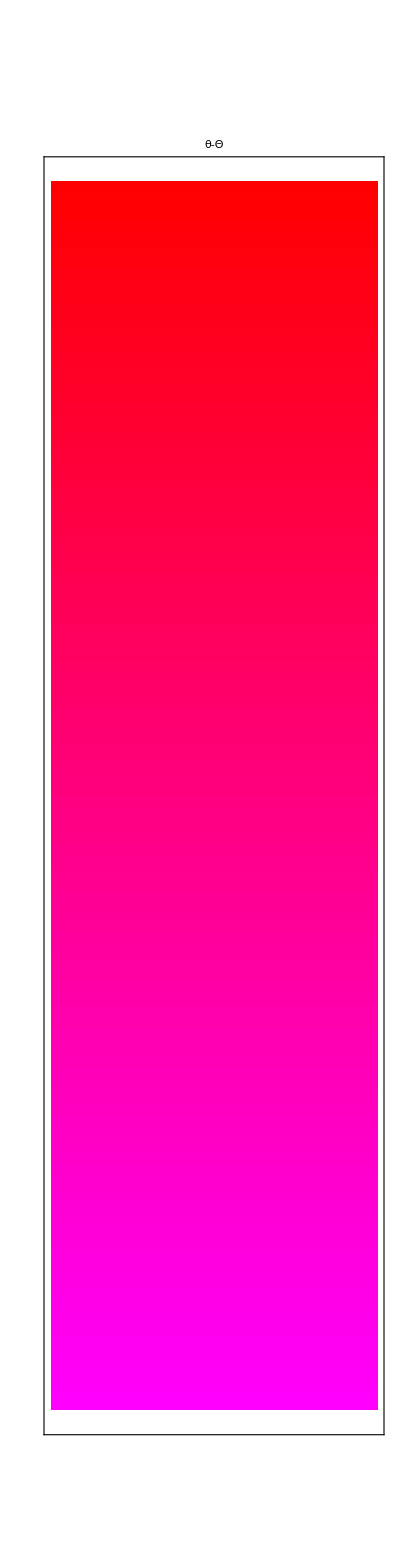
-Graphics-
-Graphics- | -Graphics- | -Graphics-

large.pdf

```mathematica
thr=Pi/8;cf=Piecewise[{{White,#<-thr},{Blend[{pblue,pgreen},(#+thr)/(thr)],#≤0},{Blend[{pgreen,pred},(#)/(thr)],#≤thr},{White,#>thr}}]&;
p1=ListPlot[Mean[table],Frame->True,Axes->False,FrameLabel->{K'',OverBar[R^2]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[24,Black],AspectRatio->1/3,ImageSize->750,Joined->True,PlotLegends->Placed[{"Uncorrelated noise","Common noise","No noise"},{0.2,0.6}],PlotStyle->{Directive[ColorData[97,"ColorList"][[3]],AbsoluteThickness[3]],Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[3]],Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[3]]}];
p2=rasterizeBackground[ListDensityPlot[Transpose[Pi+#-Arg[Total[Exp[I*data1[[3;;-10]]]]]&/@Reverse[SortBy[data1[[3;;-1,All]],Last]]],FrameTicks->{{Table[{i,Floor[i*dt]},{i,0,Length[data1[[1]]],Floor[Length[data1[[1]]]/5]}],Table[{i,""},{i,0,Length[data1[[1]]],Floor[Length[data1[[1]]]/5]}]},{Table[i,{i,0,n,Floor[n/5]}],Table[{i,""},{i,0,n,Floor[n/5]}]}},FrameLabel->{{t,None},{i,None}},PlotRange->All,InterpolationOrder->0,AspectRatio->2/3,ColorFunctionScaling->False,ColorFunction->(cf[Mod[#,2*Pi]-Pi]&),FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[24,Black],ImageSize->390,ImagePadding->{{95,15},{75,55}},PlotRangeClipping->None]];
p3=rasterizeBackground[ListDensityPlot[Transpose[Pi+#-Arg[Total[Exp[I*data2[[3;;-10]]]]]&/@Reverse[SortBy[data2[[3;;-1,All]],Last]]],FrameTicks->{{Table[{i,""},{i,0,Length[data2[[1]]],Floor[Length[data2[[1]]]/5]}],Table[{i,""},{i,0,Length[data2[[1]]],Floor[Length[data2[[1]]]/5]}]},{Table[i,{i,0,n,Floor[n/5]}],Table[{i,""},{i,0,n,Floor[n/5]}]}},FrameLabel->{{None,None},{i,None}},PlotRange->All,InterpolationOrder->0,AspectRatio->2/3,ColorFunctionScaling->False,ColorFunction->(cf[Mod[#,2*Pi]-Pi]&),FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[24,Black],ImageSize->390,ImagePadding->{{15,95},{75,55}},PlotRangeClipping->None]];
p=Grid[{{p1},{Grid[{{p2,p3,MatrixPlot[Table[cf[-thr+thr*(i-1)/100],{i,1,100},{j,1,10}],PlotRangePadding->None,FrameTicks->{{None,{{1,DisplayForm[RowBox[{"π","/",Pi/thr}]]},{25,DisplayForm[RowBox[{"π","/",Pi/thr/2}]]},{50,0},{75,DisplayForm[RowBox[{"-π","/",Pi/thr/2}]]},{100,DisplayForm[RowBox[{"-π","/",Pi/thr}]]}}},{None,None}},LabelStyle->Directive[18,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->10,ImageSize->{Automatic,150},PlotLabel->θ-Θ,PlotRange->{{1,100},{1,10}}]}}]}}]
Export["large.pdf",p]
```

```mathematica
plots={};
Monitor[Do[filebase="data/noise/"<>ToString[m]<>"/";
strlst=ReadList[filebase<>"correlated50.out",String];
lst=StringSplit[First[strlst]];
n=2+ToExpression[lst[[2]]];
delta=ToExpression[lst[[6]]];
dt=Internal`StringToDouble[lst[[10]]];
Nt=Floor[Internal`StringToDouble[lst[[8]]]/dt];
n0=Floor[Internal`StringToDouble[lst[[9]]]/dt];
t1=Internal`StringToDouble[lst[[8]]];
t2=Internal`StringToDouble[lst[[9]]];
data1=Transpose[Partition[BinaryReadList[filebase<>"correlated50.dat","Real64"],n],{2,1}];
frequencies1=Flatten[Import[filebase<>"correlated50frequencies.dat"]];
data2=Transpose[Partition[BinaryReadList[filebase<>"uncorrelated50.dat","Real64"],n],{2,1}];
frequencies2=Flatten[Import[filebase<>"uncorrelated50frequencies.dat"]];
p1=ListPlot[Mean[table],Frame->True,Axes->False,FrameLabel->{K'',OverBar[R^2]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[24,Black],AspectRatio->1/3,ImageSize->750,Joined->True,PlotLegends->Placed[{"Noiseless","Uncorrelated","Common"},{0.2,0.6}],PlotStyle->Directive[AbsoluteThickness[3]]];
thr=Pi/8;cf=Piecewise[{{White,#<-thr},{Blend[{pblue,pgreen},(#+thr)/(thr)],#≤0},{Blend[{pgreen,pred},(#)/(thr)],#≤thr},{White,#>thr}}]&;
p1=ListPlot[Mean[table],Frame->True,Axes->False,FrameLabel->{K'',OverBar[R^2]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[24,Black],AspectRatio->1/3,ImageSize->750,Joined->True,PlotLegends->Placed[{"Uncorrelated noise","Common noise","No noise"},{0.2,0.6}],PlotStyle->{Directive[ColorData[97,"ColorList"][[3]],AbsoluteThickness[3]],Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[3]],Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[3]]}];
p2=rasterizeBackground[ListDensityPlot[Transpose[Pi+#-Arg[Total[Exp[I*data1[[3;;-10]]]]]&/@Reverse[SortBy[data1[[3;;-1,All]],Last]]],FrameTicks->{{Table[{i,Floor[i*dt]},{i,0,Length[data1[[1]]],Floor[Length[data1[[1]]]/5]}],Table[{i,""},{i,0,Length[data1[[1]]],Floor[Length[data1[[1]]]/5]}]},{Table[i,{i,0,n,Floor[n/5]}],Table[{i,""},{i,0,n,Floor[n/5]}]}},FrameLabel->{{t,None},{i,None}},PlotRange->All,InterpolationOrder->0,AspectRatio->2/3,ColorFunctionScaling->False,ColorFunction->(cf[Mod[#,2*Pi]-Pi]&),FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[24,Black],ImageSize->390,ImagePadding->{{95,15},{75,55}},PlotRangeClipping->None]];
p3=rasterizeBackground[ListDensityPlot[Transpose[Pi+#-Arg[Total[Exp[I*data2[[3;;-10]]]]]&/@Reverse[SortBy[data2[[3;;-1,All]],Last]]],FrameTicks->{{Table[{i,""},{i,0,Length[data2[[1]]],Floor[Length[data2[[1]]]/5]}],Table[{i,""},{i,0,Length[data2[[1]]],Floor[Length[data2[[1]]]/5]}]},{Table[i,{i,0,n,Floor[n/5]}],Table[{i,""},{i,0,n,Floor[n/5]}]}},FrameLabel->{{None,None},{i,None}},PlotRange->All,InterpolationOrder->0,AspectRatio->2/3,ColorFunctionScaling->False,ColorFunction->(cf[Mod[#,2*Pi]-Pi]&),FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[24,Black],ImageSize->390,ImagePadding->{{15,95},{75,55}},PlotRangeClipping->None]];
p=Grid[{{p1},{Grid[{{p2,p3,MatrixPlot[Table[cf[-thr+thr*(i-1)/100],{i,1,100},{j,1,10}],PlotRangePadding->None,FrameTicks->{{None,{{1,thr},{25,thr/2},{50,0},{75,-thr/2},{100,-thr}}},{None,None}},LabelStyle->Directive[18,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->10,ImageSize->{Automatic,200},PlotLabel->θ-Θ,PlotRange->{{1,100},{1,10}}]}}]}}];
AppendTo[plots,p];,{m,11,20}],m]
Do[Export["large"<>ToString[m+10]<>".pdf",plots[[m]]];,{m,1,10}]
```